```mathematica
file="/Volumes/marshallShare/SplitDrive_Yorkeys/Landscapes/LandOriginal/Yorkeys01.csv";
raw=Import[file];
{thresholdX,fixed}={145.7125,{150,-17}};
yk=Cases[raw,a_/;a[[1]]>thresholdX->a];
tp=Cases[raw,a_/;a[[1]]≤thresholdX->a];
```

```mathematica
ListPlot[tp,AspectRatio->1]
```

```mathematica
distancesYK=EuclideanDistance[fixed,#]&/@yk;
orderYK=Ordering[distancesYK];
distancesTP=EuclideanDistance[fixed,#]&/@tp;
orderTP=Ordering[distancesTP];
flat=Flatten[{yk[[orderYK]],tp[[orderTP]]},1];
rows=Flatten/@({Range[0,Length[flat]-1],flat}//Transpose);
csvReady=Prepend[rows,{"ID","Latitude", "Longitude"}]
(*Export["Yorkeys01_S.csv",csvReady]*)
```

{{ID,Latitude,Longitude},{0,145.727,-16.8125},{1,145.727,-16.8122},{2,145.727,-16.812},{3,145.727,-16.8117},{4,145.727,-16.8117},2185,{2190,145.693,-16.8074},{2191,145.693,-16.8073},{2192,145.693,-16.8076},{2193,145.693,-16.8066},{2194,145.692,-16.8069}}
 |  |  |  |

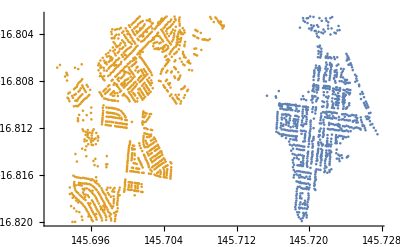

```mathematica
ListPlot[{yk,tp}]
```

```mathematica
Length[yk]+Length[tp]
```

2195